## Finite T, B background code defs

### EoMs

Coupled region eoms - rearranged to get rid of cancellations of large/small numerical factors in the UV!!!

```mathematica
Clear[eomsFTB]
eomsFTB={λ'[A]==-1/2 √3 λ[A] √(1/f[A](6 f[A] (2+W'[A])+f'[A] (3+W'[A])-q[A]^2 (Vg[λ[A]]+x q[A] Vf[λ[A],τ[A]] √((1+B^2 ⅇ^(-4 A) wB[λ[A]]^2)/(q[A]^2+f[A] κ[λ[A]] τ'[A]^2))))),q'[A]==1/6 q[A] (-(2 q[A]^2 Vg[λ[A]])/f[A]+(6 f'[A])/f[A]+6 (4+W'[A])-(x q[A]^3 Vf[λ[A],τ[A]] (2+3 B^2 ⅇ^(-4 A) wB[λ[A]]^2))/(f[A] √((1+B^2 ⅇ^(-4 A) wB[λ[A]]^2) (q[A]^2+f[A] κ[λ[A]] τ'[A]^2)))-(x q[A] Vf[λ[A],τ[A]] (1+2 B^2 ⅇ^(-4 A) wB[λ[A]]^2) κ[λ[A]] τ'[A]^2)/(√((1+B^2 ⅇ^(-4 A) wB[λ[A]]^2) (q[A]^2+f[A] κ[λ[A]] τ'[A]^2)))),f''[A]==f'[A]^2/f[A]-B^2 ⅇ^(-4 A) x q[A] Vf[λ[A],τ[A]] wB[λ[A]]^2 √((q[A]^2+f[A] κ[λ[A]] τ'[A]^2)/(1+B^2 ⅇ^(-4 A) wB[λ[A]]^2))-(q[A] f'[A] (x q[A]^2 Vf[λ[A],τ[A]] (2+3 B^2 ⅇ^(-4 A) wB[λ[A]]^2)+x f[A] Vf[λ[A],τ[A]] (1+2 B^2 ⅇ^(-4 A) wB[λ[A]]^2) κ[λ[A]] τ'[A]^2+2 q[A] Vg[λ[A]] √((1+B^2 ⅇ^(-4 A) wB[λ[A]]^2) (q[A]^2+f[A] κ[λ[A]] τ'[A]^2))))/(6 f[A] √((1+B^2 ⅇ^(-4 A) wB[λ[A]]^2) (q[A]^2+f[A] κ[λ[A]] τ'[A]^2))),W''[A]==-(B^2 ⅇ^(-4 A) x q[A]^3 Vf[λ[A],τ[A]] wB[λ[A]]^2)/(2 f[A] √((1+B^2 ⅇ^(-4 A) wB[λ[A]]^2) (q[A]^2+f[A] κ[λ[A]] τ'[A]^2)))+(q[A]^2 W'[A] (-2 Vg[λ[A]]-(x q[A] Vf[λ[A],τ[A]] (2+3 B^2 ⅇ^(-4 A) wB[λ[A]]^2))/(√((1+B^2 ⅇ^(-4 A) wB[λ[A]]^2) (q[A]^2+f[A] κ[λ[A]] τ'[A]^2)))))/(6 f[A])+τ'[A]^2 (-(B^2 ⅇ^(-4 A) x q[A] Vf[λ[A],τ[A]] wB[λ[A]]^2 κ[λ[A]])/(2 √((1+B^2 ⅇ^(-4 A) wB[λ[A]]^2) (q[A]^2+f[A] κ[λ[A]] τ'[A]^2)))-(x q[A] Vf[λ[A],τ[A]] (1+2 B^2 ⅇ^(-4 A) wB[λ[A]]^2) κ[λ[A]] W'[A])/(6 √((1+B^2 ⅇ^(-4 A) wB[λ[A]]^2) (q[A]^2+f[A] κ[λ[A]] τ'[A]^2)))),τ''[A]==1/12 (-(6 κ[λ[A]] f'[A] τ'[A]^3)/q[A]^2-(12 f[A] κ[λ[A]] W'[A] τ'[A]^3)/q[A]^2+1/(q[A]^2 (1+B^2 ⅇ^(-4 A) wB[λ[A]]^2))6 √3 B^2 ⅇ^(-4 A) wB[λ[A]] λ[A] wB'[λ[A]] τ'[A] (q[A]^2+f[A] κ[λ[A]] τ'[A]^2) √(1/f[A](-q[A]^2 Vg[λ[A]]+6 f[A] (2+W'[A])+f'[A] (3+W'[A])-ⅇ^logVf[λ[A],τ[A]] x q[A]^3 √((1+B^2 ⅇ^(-4 A) wB[λ[A]]^2)/(q[A]^2+f[A] κ[λ[A]] τ'[A]^2))))+1/(q[A]^2 κ[λ[A]])3 √3 λ[A] κ'[λ[A]] τ'[A] (2 q[A]^2+f[A] κ[λ[A]] τ'[A]^2) √(1/f[A](-q[A]^2 Vg[λ[A]]+6 f[A] (2+W'[A])+f'[A] (3+W'[A])-ⅇ^logVf[λ[A],τ[A]] x q[A]^3 √((1+B^2 ⅇ^(-4 A) wB[λ[A]]^2)/(q[A]^2+f[A] κ[λ[A]] τ'[A]^2))))-(2 τ'[A] (2 q[A]^6 Vg[λ[A]] (1+B^2 ⅇ^(-4 A) wB[λ[A]]^2)+24 f[A]^2 q[A]^2 κ[λ[A]] τ'[A]^2+12 f[A]^3 (2+B^2 ⅇ^(-4 A) wB[λ[A]]^2) κ[λ[A]]^2 τ'[A]^4+ⅇ^logVf[λ[A],τ[A]] x q[A]^5 (2+3 B^2 ⅇ^(-4 A) wB[λ[A]]^2) √((1+B^2 ⅇ^(-4 A) wB[λ[A]]^2) (q[A]^2+f[A] κ[λ[A]] τ'[A]^2))+ⅇ^logVf[λ[A],τ[A]] x f[A] q[A]^3 (1+2 B^2 ⅇ^(-4 A) wB[λ[A]]^2) κ[λ[A]] τ'[A]^2 √((1+B^2 ⅇ^(-4 A) wB[λ[A]]^2) (q[A]^2+f[A] κ[λ[A]] τ'[A]^2))+2 f[A] q[A]^4 (Vg[λ[A]] κ[λ[A]] τ'[A]^2+B^2 ⅇ^(-4 A) wB[λ[A]]^2 (-6+Vg[λ[A]] κ[λ[A]] τ'[A]^2))))/(f[A] q[A]^2 (1+B^2 ⅇ^(-4 A) wB[λ[A]]^2) (q[A]^2+f[A] κ[λ[A]] τ'[A]^2))+(12 (q[A]^2+f[A] κ[λ[A]] τ'[A]^2) Derivative[0,1][logVf][λ[A],τ[A]])/(f[A] κ[λ[A]])+1/q[A]^2 6 √3 λ[A] τ'[A] (q[A]^2+f[A] κ[λ[A]] τ'[A]^2) √(1/f[A](-q[A]^2 Vg[λ[A]]+6 f[A] (2+W'[A])+f'[A] (3+W'[A])-ⅇ^logVf[λ[A],τ[A]] x q[A]^3 √((1+B^2 ⅇ^(-4 A) wB[λ[A]]^2)/(q[A]^2+f[A] κ[λ[A]] τ'[A]^2)))) Derivative[1,0][logVf][λ[A],τ[A]])};
```

Horizon expansions

Collect[horexps[[8,2]]/.nC→0,ϵ,Simplify[#/.Vf→Function[{λ,τ},Exp[logVf[λ,τ]]],logVf[λh,τh]>0&&Vf[λh,τh]>0&&wμ[λh]>0&&x>0]&]/.{ⅇ^logVf[λh,τh]->Vf[λh,τh],ⅇ^(2 logVf[λh,τh])->Vf[λh,τh]^2}

```mathematica
qhexp=-(√6 √(2 Vg[λh] (1+B^2 wB[λh]^2)+x Vf[λh,τh] √(1+B^2 wB[λh]^2) (2+3 B^2 wB[λh]^2)))/(√(4 Vg[λh]^2 (1+B^2 wB[λh]^2)-x^2 Vf[λh,τh]^2 (2+3 B^2 wB[λh]^2)^2));
```

```mathematica
horexps={q[ϵ]==qh-(qh ϵ (B^2 qh^4 x^2 Vf[λh,τh]^2 wB[λh]^2 κ[λh] (8+12 B^4 wB[λh]^4-12 B^2 λh^2 wB'[λh]^2+wB[λh]^2 (20 B^2-9 B^4 λh^2 wB'[λh]^2))-4 qh^4 x Vf[λh,τh] √(1+B^2 wB[λh]^2) (4+11 B^2 wB[λh]^2+7 B^4 wB[λh]^4) (Derivative[0,1][logVf][λh,τh])^2-qh^2 x Vf[λh,τh] κ[λh] (64 √(1+B^2 wB[λh]^2)+8 B^2 (15+qh^2 Vg[λh]) wB[λh]^2 √(1+B^2 wB[λh]^2)+8 B^4 (9+qh^2 Vg[λh]) wB[λh]^4 √(1+B^2 wB[λh]^2)+18 B^6 qh^2 x λh^2 Vf[λh,τh] wB[λh]^5 wB'[λh] Derivative[1,0][logVf][λh,τh]-18 B^2 qh^2 λh^2 wB[λh] wB'[λh] (√(1+B^2 wB[λh]^2) Vg'[λh]-x Vf[λh,τh] Derivative[1,0][logVf][λh,τh])+3 B^4 qh^2 λh^2 wB[λh]^3 wB'[λh] (-5 √(1+B^2 wB[λh]^2) Vg'[λh]+12 x Vf[λh,τh] Derivative[1,0][logVf][λh,τh]))-(1+B^2 wB[λh]^2) κ[λh] (-64 qh^2 Vg[λh] (1+B^2 wB[λh]^2)+9 B^4 qh^4 x^2 λh^2 Vf[λh,τh]^2 wB[λh]^4 (Derivative[1,0][logVf][λh,τh])^2+6 (32+qh^4 λh^2 Vg'[λh]^2-2 qh^4 x λh^2 Vf[λh,τh] √(1+B^2 wB[λh]^2) Vg'[λh] Derivative[1,0][logVf][λh,τh]+qh^4 x^2 λh^2 Vf[λh,τh]^2 (Derivative[1,0][logVf][λh,τh])^2)+3 B^2 wB[λh]^2 (64+2 qh^4 λh^2 Vg'[λh]^2-5 qh^4 x λh^2 Vf[λh,τh] √(1+B^2 wB[λh]^2) Vg'[λh] Derivative[1,0][logVf][λh,τh]+5 qh^4 x^2 λh^2 Vf[λh,τh]^2 (Derivative[1,0][logVf][λh,τh])^2))))/(24 (1+B^2 wB[λh]^2)^(3/2) (2 (-1+qh^2 Vg[λh]) √(1+B^2 wB[λh]^2)-qh^2 x Vf[λh,τh] (2+3 B^2 wB[λh]^2)) κ[λh]),λ[ϵ]==λh+3/8 qh^2 ϵ λh^2 (-Vg'[λh]+1/(√(1+B^2 wB[λh]^2))x Vf[λh,τh] (B^2 wB[λh] wB'[λh]+Derivative[1,0][logVf][λh,τh]+B^2 wB[λh]^2 Derivative[1,0][logVf][λh,τh])),f[ϵ]==ϵ,Derivative[1][f][ϵ]==1-(ϵ (B^2 qh^4 x^2 Vf[λh,τh]^2 wB[λh]^2 κ[λh] (32+48 B^4 wB[λh]^4-12 B^2 λh^2 wB'[λh]^2+wB[λh]^2 (80 B^2-9 B^4 λh^2 wB'[λh]^2))-4 qh^4 x Vf[λh,τh] √(1+B^2 wB[λh]^2) (4+11 B^2 wB[λh]^2+7 B^4 wB[λh]^4) (Derivative[0,1][logVf][λh,τh])^2-qh^2 x Vf[λh,τh] κ[λh] (256 √(1+B^2 wB[λh]^2)+32 B^2 (18+qh^2 Vg[λh]) wB[λh]^2 √(1+B^2 wB[λh]^2)+16 B^4 (21+2 qh^2 Vg[λh]) wB[λh]^4 √(1+B^2 wB[λh]^2)+18 B^6 qh^2 x λh^2 Vf[λh,τh] wB[λh]^5 wB'[λh] Derivative[1,0][logVf][λh,τh]-18 B^2 qh^2 λh^2 wB[λh] wB'[λh] (√(1+B^2 wB[λh]^2) Vg'[λh]-x Vf[λh,τh] Derivative[1,0][logVf][λh,τh])+3 B^4 qh^2 λh^2 wB[λh]^3 wB'[λh] (-5 √(1+B^2 wB[λh]^2) Vg'[λh]+12 x Vf[λh,τh] Derivative[1,0][logVf][λh,τh]))-(1+B^2 wB[λh]^2) κ[λh] (-256 qh^2 Vg[λh] (1+B^2 wB[λh]^2)+9 B^4 qh^4 x^2 λh^2 Vf[λh,τh]^2 wB[λh]^4 (Derivative[1,0][logVf][λh,τh])^2+6 (64+qh^4 λh^2 Vg'[λh]^2-2 qh^4 x λh^2 Vf[λh,τh] √(1+B^2 wB[λh]^2) Vg'[λh] Derivative[1,0][logVf][λh,τh]+qh^4 x^2 λh^2 Vf[λh,τh]^2 (Derivative[1,0][logVf][λh,τh])^2)+3 B^2 wB[λh]^2 (128+2 qh^4 λh^2 Vg'[λh]^2-5 qh^4 x λh^2 Vf[λh,τh] √(1+B^2 wB[λh]^2) Vg'[λh] Derivative[1,0][logVf][λh,τh]+5 qh^4 x^2 λh^2 Vf[λh,τh]^2 (Derivative[1,0][logVf][λh,τh])^2))))/(24 (1+B^2 wB[λh]^2)^(3/2) (2 (-1+qh^2 Vg[λh]) √(1+B^2 wB[λh]^2)-qh^2 x Vf[λh,τh] (2+3 B^2 wB[λh]^2)) κ[λh]),W[ϵ]==(B^2 qh^2 x ϵ Vf[λh,τh] wB[λh]^2)/(2 √(1+B^2 wB[λh]^2)),Derivative[1][W][ϵ]==(B^2 qh^2 x Vf[λh,τh] wB[λh]^2)/(2 √(1+B^2 wB[λh]^2))+(B^2 qh^2 x ϵ Vf[λh,τh] wB[λh] (18 B^6 qh^4 x^2 λh^2 Vf[λh,τh]^2 wB[λh]^6 κ[λh] wB'[λh] Derivative[1,0][logVf][λh,τh]+18 B^2 qh^2 λh^2 wB[λh]^2 κ[λh] wB'[λh] ((-3+3 qh^2 Vg[λh]-2 qh^2 x Vf[λh,τh] √(1+B^2 wB[λh]^2)) Vg'[λh]+x Vf[λh,τh] (5 qh^2 x Vf[λh,τh]+4 √(1+B^2 wB[λh]^2)-4 qh^2 Vg[λh] √(1+B^2 wB[λh]^2)) Derivative[1,0][logVf][λh,τh])+36 qh^2 λh^2 κ[λh] wB'[λh] ((-1+qh^2 Vg[λh]-qh^2 x Vf[λh,τh] √(1+B^2 wB[λh]^2)) Vg'[λh]+x Vf[λh,τh] (qh^2 x Vf[λh,τh]+√(1+B^2 wB[λh]^2)-qh^2 Vg[λh] √(1+B^2 wB[λh]^2)) Derivative[1,0][logVf][λh,τh])+3 B^4 qh^2 λh^2 wB[λh]^4 κ[λh] wB'[λh] ((-6+6 qh^2 Vg[λh]+qh^2 x Vf[λh,τh] √(1+B^2 wB[λh]^2)) Vg'[λh]+12 x Vf[λh,τh] (2 qh^2 x Vf[λh,τh]+√(1+B^2 wB[λh]^2)-qh^2 Vg[λh] √(1+B^2 wB[λh]^2)) Derivative[1,0][logVf][λh,τh])+3 B^6 qh^4 x^2 Vf[λh,τh]^2 wB[λh]^7 κ[λh] (-16+3 λh^2 (Derivative[1,0][logVf][λh,τh])^2)+B^4 wB[λh]^5 (-4 qh^2 (-18+18 qh^2 Vg[λh]-13 qh^2 x Vf[λh,τh] √(1+B^2 wB[λh]^2)) (Derivative[0,1][logVf][λh,τh])^2+κ[λh] (-480-80 qh^4 x^2 Vf[λh,τh]^2-336 qh^2 x Vf[λh,τh] √(1+B^2 wB[λh]^2)-12 qh^4 λh^2 Vg'[λh]^2+9 B^2 qh^4 x^2 λh^2 Vf[λh,τh]^2 wB'[λh]^2+3 qh^2 λh^2 (-6+qh^2 x Vf[λh,τh] √(1+B^2 wB[λh]^2)) Vg'[λh] Derivative[1,0][logVf][λh,τh]+24 qh^4 x^2 λh^2 Vf[λh,τh]^2 (Derivative[1,0][logVf][λh,τh])^2+18 qh^2 x λh^2 Vf[λh,τh] √(1+B^2 wB[λh]^2) (Derivative[1,0][logVf][λh,τh])^2+2 qh^2 Vg[λh] (112+16 qh^2 x Vf[λh,τh] √(1+B^2 wB[λh]^2)+9 qh^2 λh^2 Vg'[λh] Derivative[1,0][logVf][λh,τh]-9 qh^2 x λh^2 Vf[λh,τh] √(1+B^2 wB[λh]^2) (Derivative[1,0][logVf][λh,τh])^2)))-2 wB[λh] (4 qh^2 (-9+9 qh^2 Vg[λh]-5 qh^2 x Vf[λh,τh] √(1+B^2 wB[λh]^2)) (Derivative[0,1][logVf][λh,τh])^2+κ[λh] (288+160 qh^2 x Vf[λh,τh] √(1+B^2 wB[λh]^2)+6 qh^4 λh^2 Vg'[λh]^2-18 B^2 qh^4 x^2 λh^2 Vf[λh,τh]^2 wB'[λh]^2-18 B^2 qh^2 x λh^2 Vf[λh,τh] √(1+B^2 wB[λh]^2) wB'[λh]^2-3 qh^2 λh^2 (-3+qh^2 x Vf[λh,τh] √(1+B^2 wB[λh]^2)) Vg'[λh] Derivative[1,0][logVf][λh,τh]-3 qh^4 x^2 λh^2 Vf[λh,τh]^2 (Derivative[1,0][logVf][λh,τh])^2-9 qh^2 x λh^2 Vf[λh,τh] √(1+B^2 wB[λh]^2) (Derivative[1,0][logVf][λh,τh])^2+qh^2 Vg[λh] (-160+18 B^2 qh^2 x λh^2 Vf[λh,τh] √(1+B^2 wB[λh]^2) wB'[λh]^2-9 qh^2 λh^2 Vg'[λh] Derivative[1,0][logVf][λh,τh]+9 qh^2 x λh^2 Vf[λh,τh] √(1+B^2 wB[λh]^2) (Derivative[1,0][logVf][λh,τh])^2)))+B^2 wB[λh]^3 (-4 qh^2 (-36+36 qh^2 Vg[λh]-23 qh^2 x Vf[λh,τh] √(1+B^2 wB[λh]^2)) (Derivative[0,1][logVf][λh,τh])^2+κ[λh] (-1056-32 qh^4 x^2 Vf[λh,τh]^2-672 qh^2 x Vf[λh,τh] √(1+B^2 wB[λh]^2)-24 qh^4 λh^2 Vg'[λh]^2+48 B^2 qh^4 x^2 λh^2 Vf[λh,τh]^2 wB'[λh]^2+18 B^2 qh^2 x λh^2 Vf[λh,τh] √(1+B^2 wB[λh]^2) wB'[λh]^2+9 qh^2 λh^2 (-4+qh^2 x Vf[λh,τh] √(1+B^2 wB[λh]^2)) Vg'[λh] Derivative[1,0][logVf][λh,τh]+21 qh^4 x^2 λh^2 Vf[λh,τh]^2 (Derivative[1,0][logVf][λh,τh])^2+36 qh^2 x λh^2 Vf[λh,τh] √(1+B^2 wB[λh]^2) (Derivative[1,0][logVf][λh,τh])^2+Vg[λh] (-18 B^2 qh^4 x λh^2 Vf[λh,τh] √(1+B^2 wB[λh]^2) wB'[λh]^2+4 qh^2 (136+8 qh^2 x Vf[λh,τh] √(1+B^2 wB[λh]^2)+9 qh^2 λh^2 Vg'[λh] Derivative[1,0][logVf][λh,τh]-9 qh^2 x λh^2 Vf[λh,τh] √(1+B^2 wB[λh]^2) (Derivative[1,0][logVf][λh,τh])^2))))))/(96 (1+B^2 wB[λh]^2)^2 (3 B^2 qh^2 x Vf[λh,τh] wB[λh]^2+2 (qh^2 x Vf[λh,τh]+√(1+B^2 wB[λh]^2)-qh^2 Vg[λh] √(1+B^2 wB[λh]^2))) κ[λh]),τ[ϵ]==τh+(qh^2 ϵ Derivative[0,1][logVf][λh,τh])/κ[λh],Derivative[1][τ][ϵ]==(qh^2 Derivative[0,1][logVf][λh,τh])/κ[λh]+1/(48 √(1+B^2 wB[λh]^2) κ[λh]^2)qh^2 ϵ (36 (-B^2 qh^2 x Vf[λh,τh] wB[λh]^2+8 √(1+B^2 wB[λh]^2)) κ[λh] Derivative[0,1][logVf][λh,τh]-(2 Derivative[0,1][logVf][λh,τh] (B^2 qh^4 x^2 Vf[λh,τh]^2 wB[λh]^2 κ[λh] (32+48 B^4 wB[λh]^4-12 B^2 λh^2 wB'[λh]^2+wB[λh]^2 (80 B^2-9 B^4 λh^2 wB'[λh]^2))-4 qh^4 x Vf[λh,τh] √(1+B^2 wB[λh]^2) (4+11 B^2 wB[λh]^2+7 B^4 wB[λh]^4) (Derivative[0,1][logVf][λh,τh])^2-qh^2 x Vf[λh,τh] κ[λh] (256 √(1+B^2 wB[λh]^2)+32 B^2 (18+qh^2 Vg[λh]) wB[λh]^2 √(1+B^2 wB[λh]^2)+16 B^4 (21+2 qh^2 Vg[λh]) wB[λh]^4 √(1+B^2 wB[λh]^2)+18 B^6 qh^2 x λh^2 Vf[λh,τh] wB[λh]^5 wB'[λh] Derivative[1,0][logVf][λh,τh]-18 B^2 qh^2 λh^2 wB[λh] wB'[λh] (√(1+B^2 wB[λh]^2) Vg'[λh]-x Vf[λh,τh] Derivative[1,0][logVf][λh,τh])+3 B^4 qh^2 λh^2 wB[λh]^3 wB'[λh] (-5 √(1+B^2 wB[λh]^2) Vg'[λh]+12 x Vf[λh,τh] Derivative[1,0][logVf][λh,τh]))-(1+B^2 wB[λh]^2) κ[λh] (-256 qh^2 Vg[λh] (1+B^2 wB[λh]^2)+9 B^4 qh^4 x^2 λh^2 Vf[λh,τh]^2 wB[λh]^4 (Derivative[1,0][logVf][λh,τh])^2+6 (64+qh^4 λh^2 Vg'[λh]^2-2 qh^4 x λh^2 Vf[λh,τh] √(1+B^2 wB[λh]^2) Vg'[λh] Derivative[1,0][logVf][λh,τh]+qh^4 x^2 λh^2 Vf[λh,τh]^2 (Derivative[1,0][logVf][λh,τh])^2)+3 B^2 wB[λh]^2 (128+2 qh^4 λh^2 Vg'[λh]^2-5 qh^4 x λh^2 Vf[λh,τh] √(1+B^2 wB[λh]^2) Vg'[λh] Derivative[1,0][logVf][λh,τh]+5 qh^4 x^2 λh^2 Vf[λh,τh]^2 (Derivative[1,0][logVf][λh,τh])^2))))/((1+B^2 wB[λh]^2) (2 (-1+qh^2 Vg[λh]) √(1+B^2 wB[λh]^2)-qh^2 x Vf[λh,τh] (2+3 B^2 wB[λh]^2)))-1/(1+B^2 wB[λh]^2)3 (-2 qh^2 Derivative[0,1][logVf][λh,τh] (3 λh^2 √(1+B^2 wB[λh]^2) Vg'[λh] κ'[λh]+2 √(1+B^2 wB[λh]^2) (Derivative[0,1][logVf][λh,τh])^2+4 √(1+B^2 wB[λh]^2) Derivative[0,2][logVf][λh,τh]-3 x λh^2 Vf[λh,τh] κ'[λh] Derivative[1,0][logVf][λh,τh])-3 B^2 qh^2 λh^2 wB[λh] wB'[λh] (-2 x Vf[λh,τh] κ'[λh] Derivative[0,1][logVf][λh,τh]+κ[λh] (√(1+B^2 wB[λh]^2) Vg'[λh] Derivative[0,1][logVf][λh,τh]-x Vf[λh,τh] (2 Derivative[0,1][logVf][λh,τh] Derivative[1,0][logVf][λh,τh]-Derivative[1,1][logVf][λh,τh])))+3 B^4 qh^2 x λh^2 Vf[λh,τh] wB[λh]^3 wB'[λh] (2 κ'[λh] Derivative[0,1][logVf][λh,τh]+κ[λh] (2 Derivative[0,1][logVf][λh,τh] Derivative[1,0][logVf][λh,τh]-Derivative[1,1][logVf][λh,τh]))+κ[λh] (Derivative[0,1][logVf][λh,τh] (32 √(1+B^2 wB[λh]^2)-3 qh^2 λh^2 √(1+B^2 wB[λh]^2) Vg'[λh] Derivative[1,0][logVf][λh,τh]+3 qh^2 x λh^2 Vf[λh,τh] (Derivative[1,0][logVf][λh,τh])^2)+3 qh^2 λh^2 (√(1+B^2 wB[λh]^2) Vg'[λh]-x Vf[λh,τh] Derivative[1,0][logVf][λh,τh]) Derivative[1,1][logVf][λh,τh])+B^4 qh^2 x Vf[λh,τh] wB[λh]^4 (6 λh^2 κ'[λh] Derivative[0,1][logVf][λh,τh] Derivative[1,0][logVf][λh,τh]+κ[λh] (Derivative[0,1][logVf][λh,τh] (4+3 λh^2 (Derivative[1,0][logVf][λh,τh])^2)-3 λh^2 Derivative[1,0][logVf][λh,τh] Derivative[1,1][logVf][λh,τh]))+B^2 wB[λh]^2 (-2 qh^2 Derivative[0,1][logVf][λh,τh] (3 λh^2 √(1+B^2 wB[λh]^2) Vg'[λh] κ'[λh]+2 √(1+B^2 wB[λh]^2) (Derivative[0,1][logVf][λh,τh])^2+4 √(1+B^2 wB[λh]^2) Derivative[0,2][logVf][λh,τh]-6 x λh^2 Vf[λh,τh] κ'[λh] Derivative[1,0][logVf][λh,τh])+κ[λh] (Derivative[0,1][logVf][λh,τh] (4 qh^2 x Vf[λh,τh]+16 √(1+B^2 wB[λh]^2)+3 B^2 qh^2 x λh^2 Vf[λh,τh] wB'[λh]^2-3 qh^2 λh^2 √(1+B^2 wB[λh]^2) Vg'[λh] Derivative[1,0][logVf][λh,τh]+6 qh^2 x λh^2 Vf[λh,τh] (Derivative[1,0][logVf][λh,τh])^2)+3 qh^2 λh^2 (√(1+B^2 wB[λh]^2) Vg'[λh]-2 x Vf[λh,τh] Derivative[1,0][logVf][λh,τh]) Derivative[1,1][logVf][λh,τh]))))};
```

UV EoMs

```mathematica
eomsUV=eomsFTB[[1;;4]]/.τ->(0&)
```

{λ'[A]==-1/2 √3 λ[A] √((-q[A]^2 (Vg[λ[A]]+x q[A] Vf[λ[A],0] √((1+B^2 ⅇ^(-4 A) wB[λ[A]]^2)/q[A]^2))+6 f[A] (2+W'[A])+f'[A] (3+W'[A]))/f[A]),q'[A]==1/6 q[A] (-(2 q[A]^2 Vg[λ[A]])/f[A]-(x q[A]^3 Vf[λ[A],0] (2+3 B^2 ⅇ^(-4 A) wB[λ[A]]^2))/(f[A] √(q[A]^2 (1+B^2 ⅇ^(-4 A) wB[λ[A]]^2)))+(6 f'[A])/f[A]+6 (4+W'[A])),f''[A]==-B^2 ⅇ^(-4 A) x q[A] Vf[λ[A],0] wB[λ[A]]^2 √(q[A]^2/(1+B^2 ⅇ^(-4 A) wB[λ[A]]^2))-(q[A] (2 q[A] Vg[λ[A]] √(q[A]^2 (1+B^2 ⅇ^(-4 A) wB[λ[A]]^2))+x q[A]^2 Vf[λ[A],0] (2+3 B^2 ⅇ^(-4 A) wB[λ[A]]^2)) f'[A])/(6 f[A] √(q[A]^2 (1+B^2 ⅇ^(-4 A) wB[λ[A]]^2)))+f'[A]^2/f[A],W''[A]==-(B^2 ⅇ^(-4 A) x q[A]^3 Vf[λ[A],0] wB[λ[A]]^2)/(2 f[A] √(q[A]^2 (1+B^2 ⅇ^(-4 A) wB[λ[A]]^2)))+(q[A]^2 (-2 Vg[λ[A]]-(x q[A] Vf[λ[A],0] (2+3 B^2 ⅇ^(-4 A) wB[λ[A]]^2))/(√(q[A]^2 (1+B^2 ⅇ^(-4 A) wB[λ[A]]^2)))) W'[A])/(6 f[A])}

```mathematica
eomUVτ=τn''[A]==-((τn[A] (q[A]^2 (1+B^2 ⅇ^(-4 A) wB[λ[A]]^2) (x Vf[λ[A],0] (2+3 B^2 ⅇ^(-4 A) wB[λ[A]]^2) κ[λ[A]]-2 √(1+B^2 ⅇ^(-4 A) wB[λ[A]]^2) (Vg[λ[A]] κ[λ[A]]+3 Derivative[0,2][logVf][λ[A],0]))+3 (f[A] (κ[λ[A]] (2 √(1+B^2 ⅇ^(-4 A) wB[λ[A]]^2)+B^2 ⅇ^(-4 A) wB[λ[A]] (6 wB[λ[A]] √(1+B^2 ⅇ^(-4 A) wB[λ[A]]^2)+√3 λ[A] √(1/f[A](1+B^2 ⅇ^(-4 A) wB[λ[A]]^2) (q[A]^2 (-Vg[λ[A]]+x Vf[λ[A],0] √(1+B^2 ⅇ^(-4 A) wB[λ[A]]^2))+6 f[A] (2+W'[A])+f'[A] (3+W'[A]))) wB'[λ[A]]))+√3 (1+B^2 ⅇ^(-4 A) wB[λ[A]]^2)^(3/2) λ[A] √(1/f[A](q[A]^2 (-Vg[λ[A]]+x Vf[λ[A],0] √(1+B^2 ⅇ^(-4 A) wB[λ[A]]^2))+6 f[A] (2+W'[A])+f'[A] (3+W'[A]))) κ'[λ[A]])+√3 (1+B^2 ⅇ^(-4 A) wB[λ[A]]^2)^(3/2) κ[λ[A]] λ[A] √(f[A] (q[A]^2 (-Vg[λ[A]]+x Vf[λ[A],0] √(1+B^2 ⅇ^(-4 A) wB[λ[A]]^2))+6 f[A] (2+W'[A])+f'[A] (3+W'[A]))) Derivative[1,0][logVf][λ[A],0])))/(6 f[A] (1+B^2 ⅇ^(-4 A) wB[λ[A]]^2)^(3/2) κ[λ[A]]))+τn'[A] (4-2/(1+B^2 ⅇ^(-4 A) wB[λ[A]]^2)+(√3 λ[A] √(1/f[A](q[A]^2 (-Vg[λ[A]]+x Vf[λ[A],0] √(1+B^2 ⅇ^(-4 A) wB[λ[A]]^2))+6 f[A] (2+W'[A])+f'[A] (3+W'[A]))) (κ'[λ[A]]+B^2 ⅇ^(-4 A) wB[λ[A]] (κ[λ[A]] wB'[λ[A]]+wB[λ[A]] κ'[λ[A]])))/(2 (1+B^2 ⅇ^(-4 A) wB[λ[A]]^2) κ[λ[A]])+1/(6 f[A] √(1+B^2 ⅇ^(-4 A) wB[λ[A]]^2))(q[A]^2 (-2 Vg[λ[A]] √(1+B^2 ⅇ^(-4 A) wB[λ[A]]^2)+x Vf[λ[A],0] (2+3 B^2 ⅇ^(-4 A) wB[λ[A]]^2))+3 √3 λ[A] √(f[A] (1+B^2 ⅇ^(-4 A) wB[λ[A]]^2) (q[A]^2 (-Vg[λ[A]]+x Vf[λ[A],0] √(1+B^2 ⅇ^(-4 A) wB[λ[A]]^2))+6 f[A] (2+W'[A])+f'[A] (3+W'[A]))) Derivative[1,0][logVf][λ[A],0]));
```

### BG code

#### Variable and function definitions for the code

This function includes the possibility to modify the tachyon potential, we may want to do this

```mathematica
potentialdefs[sc_,κsc_,wsc_,W0_,w0_,κU1_,wU1_,VgIR_,WIR_,κIR_,wIR_,W1_,κ1_,w1_,a2_]:=(
Vgf[λ_]=(Vuv[0]+Vuv[1]λ+Vuv[2] λ^2/(1+sc λ/λ0)+Vuv[0] VgIR Exp[-1/(sc λ/λ0)](sc λ/λ0)^(4/3)√Log[sc λ/λ0+1]);
Vff[λ_]=Wuv[0]+Wuv[1]λ+Wuv[2] λ^2/(1+sc λ/λ0)+Vuv[0]WIR Exp[-1/(sc λ/λ0)](1+W1  λ0/(sc λ))(sc λ/λ0)^2;
κf[λ_]=1/(κuv[0](1+κU1 sc λ/λ0+ κIR  (1+κ1 λ0/(κsc λ))Exp[-1/(κsc λ/λ0)](κsc λ/λ0)^(4/3)(Log[κsc λ/λ0+1])^(-1/2)));
wf[λ_]=w0^-1(1+wU1( sc λ/λ0)^1/(1+sc λ/λ0)+wIR (1+w1(wsc λ/λ0)^-1) Exp[-1/(wsc λ/λ0)](wsc λ/λ0)^(4/3)(Log[wsc λ/λ0+1])^-1)^-1;
Vτf[τ_]=(1+(a2-1.) τ^2)Exp[-a2 τ^2];
(*wcoeffs={wc[0]->κuv[0],wc[1]->κuv[1],wc[2]->0 };*)
βcoeffs={V0->12.,bYM[0]->2./3 11/(4. π)^2,bYM[1]->-2./3 34./(4. π)^4,b[0]->2./3(11.-2. x)/(4. π)^2,b[1]->-2./3(34.-13. x)/(4. π)^4,a[0]->3./(4. π)^2};
uvcoeffs=Chop[Simplify[{Vuv[0]->V0,Wuv[1]->(8 (-V0 b[0]+W0 x b[0]+V0 bYM[0]))/(9 x),Wuv[2]->1/(81 x)(-23 V0 b[0]^2+23 W0 x b[0]^2+36 V0 b[1]-36 W0 x b[1]+23 V0 bYM[0]^2-36 V0 bYM[1]),Vuv[1]->8/9 V0 bYM[0],Vuv[2]->1/81 V0 (23 bYM[0]^2-36 bYM[1]),λ0->8. π^2,Wuv[0]->W0,κuv[0]->3./2(V0-x W0)/12.,κuv[1]->-κU1 sc/(8. π^2)(*1/9 (-6 a[0]-5 b[0])*)(*-(8./9 b[0]+2./3. a[0])*),wuv[0]->w0}/.βcoeffs]];
ircoeffs={Vc[0]->(Vuv[0]VgIR sc (sc/λ0)^(1/3))/λ0,Vc[1]->(Vuv[0]VgIR sc (sc/λ0)^(1/3) Log[sc/λ0])/(2 λ0),Vc[2]->-(Vuv[0]VgIR sc (sc/λ0)^(1/3) Log[sc/λ0]^2)/(8 λ0),(*acir->auv[0]/κuv[0] κnuv[1]^(4/3),*)tcoeff->(16 κuv[0] κIR a2)/(VgIR Vuv[0]),a1c->a2-1.0,a2c->a2}/.uvcoeffs;
τcorr[λ_]=(4 Log[-(8 (-12+x Wuv[0]))/(9 λ (Vuv[1]-x Wuv[1]))] (Vuv[1]+12 κuv[1]-x (Wuv[1]+Wuv[0] κuv[1])))/(3 (Vuv[1]-x Wuv[1]))(*-4/3 Log[(9 λ (Vuv[1]-x Wuv[1]))/(8 Vuv[0])]-(4 κuv[1] Log[(9 λ (Vuv[1]-x Wuv[1]))/(8 Vuv[0])] Vuv[0])/(3 (Vuv[1]-x Wuv[1]))*);
Tmass2[xval_,λmval_]:=Block[{},
xsub={x->xval};
V[λ_]=Vgf[Log[λ]]-x Vff[Log[λ]]/.uvcoeffs/.xsub;
aih[λ_]=1/(κuv[0]κf[Log[λ]])/.uvcoeffs/.xsub;
λsol=Block[{$MaxExtraPrecision=1000},FindRoot[D[V[λ],λ],{λ,0.00001,λmval}]];
λmax=Chop[λ/.λsol];
Vzero=Limit[V[λ],λ->0,Direction->-1];
Return[3aih[λmax] Vzero/V[λmax]]; 
];
);
```

This is the “old” definition

The potentials defined here are
V_g=V0+8/9 V0 λ bYM[0]+(V0 λ^2 (23 bYM[0]^2-36 bYM[1]))/(81 (1+(sc λ)/λ0))+ⅇ^(-λ0/(sc λ)) V0 VgIR ((sc λ)/λ0)^(4/3) √Log[1+(sc λ)/λ0]
V_f0 = W0+(8 λ (-V0 b[0]+W0 x b[0]+V0 bYM[0]))/(9 x)+(λ^2 (-23 V0 b[0]^2+23 W0 x b[0]^2+36 V0 b[1]-36 W0 x b[1]+23 V0 bYM[0]^2-36 V0 bYM[1]))/(81 x (1+(sc λ)/λ0))+(ⅇ^(-λ0/(sc λ)) sc^2 V0 WIR λ^2 (1+(W1 λ0)/(sc λ)))/λ0^2
a = 1
κ^-1 = 1/8 (V0-W0 x) (1+(sc κU1 λ)/λ0+(ⅇ^(-λ0/(κsc λ)) κIR ((κsc λ)/λ0)^(4/3) (1+(κ1 λ0)/(κsc λ)))/(√Log[1+(κsc λ)/λ0]))
w^-1=w0 (1+(sc wU1 λ)/((1+(sc λ)/λ0) λ0)+(ⅇ^(-λ0/(wsc λ)) wIR ((wsc λ)/λ0)^(4/3) (1+(w1 λ0)/(wsc λ)))/Log[1+(wsc λ)/λ0])
They have V_f0 ~ λ^2, and log corrections to ensure that meson radial trajectories for squared masses are asymptotically linear
Plugging in the UV and other fixed parameters at x=1 (and setting λ0=8 π^2) one gets
V_g=12.+0.495348 λ+(0.0121961 λ^2)/(1+0.0126651 sc λ)+0.0354265 ⅇ^(-78.9568/(sc λ)) VgIR (sc λ)^(4/3) √Log[1+0.0126651 sc λ]
V_f0 =W0+0.888889 (0.101321+0.0379954 W0) λ+(0.0123457 (0.346905+0.0534152 W0) λ^2)/(1+0.0126651 sc λ)+0.00192487 ⅇ^(-78.9568/(sc λ)) sc^2 WIR (1+(78.9568 W1)/(sc λ)) λ^2
a = 1
κ^-1 =0.125 (12.-1. W0) (1+0.0126651 sc κU1 λ+(0.00295221 ⅇ^(-78.9568/(κsc λ)) κIR (1+(78.9568 κ1)/(κsc λ)) (κsc λ)^(4/3))/(√Log[1+0.0126651 κsc λ]))
w^-1=w0 (1+(0.0126651 sc wU1 λ)/(1+0.0126651 sc λ)+(0.00295221 ⅇ^(-78.9568/(wsc λ)) wIR (1+(78.9568 w1)/(wsc λ)) (wsc λ)^(4/3))/Log[1+0.0126651 wsc λ])

```mathematica
Clear[potentialdefs]
potentialdefs[sc_,κsc_,wsc_,W0_,w0_,κU1_,wU1_,VgIR_,WIR_,κIR_,wIR_,W1_,κ1_,w1_]:=(
Vgf[λ_]=(Vuv[0]+Vuv[1]λ+Vuv[2] λ^2/(1+sc λ/λ0)+Vuv[0] VgIR Exp[-1/(sc λ/λ0)](sc λ/λ0)^(4/3)√Log[sc λ/λ0+1]);
Vff[λ_]=Wuv[0]+Wuv[1]λ+Wuv[2] λ^2/(1+sc λ/λ0)+Vuv[0]WIR Exp[-1/(sc λ/λ0)](1+W1  λ0/(sc λ))(sc λ/λ0)^2;
κf[λ_]=1/(κuv[0](1+κU1 sc λ/λ0+ κIR  (1+κ1 λ0/(κsc λ))Exp[-1/(κsc λ/λ0)](κsc λ/λ0)^(4/3)(Log[κsc λ/λ0+1])^(-1/2)));
wf[λ_]=w0^-1(1+wU1( sc λ/λ0)^1/(1+sc λ/λ0)+wIR (1+w1(wsc λ/λ0)^-1) Exp[-1/(wsc λ/λ0)](wsc λ/λ0)^(4/3)(Log[wsc λ/λ0+1])^-1)^-1;
Vτf[τ_]=Exp[- τ^2];
(*wcoeffs={wc[0]->κuv[0],wc[1]->κuv[1],wc[2]->0 };*)
βcoeffs={V0->12.,bYM[0]->2./3 11/(4. π)^2,bYM[1]->-2./3 34./(4. π)^4,b[0]->2./3(11.-2. x)/(4. π)^2,b[1]->-2./3(34.-13. x)/(4. π)^4(*,a[0]->3./(4. π)^2*)};
uvcoeffs=Chop[Simplify[{Vuv[0]->V0,Wuv[1]->(8 (-V0 b[0]+W0 x b[0]+V0 bYM[0]))/(9 x),Wuv[2]->1/(81 x)(-23 V0 b[0]^2+23 W0 x b[0]^2+36 V0 b[1]-36 W0 x b[1]+23 V0 bYM[0]^2-36 V0 bYM[1]),Vuv[1]->8/9 V0 bYM[0],Vuv[2]->1/81 V0 (23 bYM[0]^2-36 bYM[1]),λ0->8. π^2,Wuv[0]->W0,κuv[0]->3./2(V0-x W0)/12.,κuv[1]->-κU1 sc/(8. π^2)(*1/9 (-6 a[0]-5 b[0])*)(*-(8./9 b[0]+2./3. a[0])*),wuv[0]->w0}/.βcoeffs]];
ircoeffs={Vc[0]->(Vuv[0]VgIR sc (sc/λ0)^(1/3))/λ0,Vc[1]->(Vuv[0]VgIR sc (sc/λ0)^(1/3) Log[sc/λ0])/(2 λ0),Vc[2]->-(Vuv[0]VgIR sc (sc/λ0)^(1/3) Log[sc/λ0]^2)/(8 λ0),(*acir->auv[0]/κuv[0] κnuv[1]^(4/3),*)tcoeff->(16 κuv[0] κIR)/(VgIR Vuv[0]),a1c->0.,a2c->1.}/.uvcoeffs;
τcorr[λ_]=-4/3 Log[(9 λ (Vuv[1]-x Wuv[1]))/(8 (Vuv[0]-x Wuv[0]))]-(4 κuv[1] Log[(9 λ (Vuv[1]-x Wuv[1]))/(8 (Vuv[0]-x Wuv[0]))] (Vuv[0]-x Wuv[0]))/(3  (Vuv[1]-x Wuv[1]));(* NB: no κuv[0] here, κuv[1] is the relative coefficient *)
Tmass2[xval_,λmval_]:=Block[{},
xsub={x->xval};
V[λ_]=Vgf[λ]-x Vff[λ]/.uvcoeffs/.xsub;
aih[λ_]=1/(κuv[0]κf[λ])/.uvcoeffs/.xsub;
λsol=Block[{$MaxExtraPrecision=1000},FindRoot[D[V[λ],λ],{λ,0.00001,λmval}]];
λmax=Chop[λ/.λsol];
Vzero=Limit[V[λ],λ->0,Direction->-1];
Return[3aih[λmax] Vzero/V[λmax]];
];
);
```

```mathematica
ΛUVc2[Ac_,δA_]:=(
lval=Sqrt[12/(Vuv[0]-x Wuv[0])]/.uvcoeffs/.xBsub;
la[A_]=1/lval Exp[A-1/(λ b[0])+(b[1] Log[b[0] λ])/b[0]^2/.βcoeffs/.λ->λUV[A]/.xBsub];
a1=Ac-5.-δA;
a2=Ac-5.;
lab=(la[a1] λUV[a2]-la[a2] λUV[a1])/(λUV[a2]-λUV[a1])
);
Acopt[x_]=Piecewise[{{1000.,x<4.4},{5000.,4.4≤ x<4.9}},10000.];
δAopt[x_]=Piecewise[{{200.,x<4.4},{500.,4.4≤ x<4.9}},1000.];
```

#### The code

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
```

Changes wrt MMA 11.2 version:
AccuracyGoal reduced from 500 to 100 in the main call and the the tachyon UV call

```mathematica
solFTB[xv_,Bv_,λhin_,τhin_,ϵv_,AUVc1_,AUVc2_]:=Block[{},
xBsub={x->xv,B->Bv};
{Vgi[λ_],Vfi[λ_],κi[λ_],wBi[λ_],wμi[λ_]}={Vgf[λ],Vff[λ],κf[λ],wf[λ],wf[λ]}/.uvcoeffs/.xBsub;
Vτi=Vτf;
logVτi[τ_]=Log[1+a1c τ^2]-a2c τ^2/.ircoeffs;
fsubs=Union[xBsub,{Vg->Function[λ,Vgi[λ]],Vf->Function[{λ,τ},Vfi[λ]Vτi[τ]],logVf->Function[{λ,τ},Log[Vfi[λ]]+logVτi[τ]],Vf0->Function[{λ},Vfi[λ]],κ->Function[{λ},κi[λ]],wB->Function[{λ},wBi[λ]],wμ->Function[{λ},wμi[λ]]}/.uvcoeffs/.xBsub];
mainsol=First[NDSolve[Join[eomsFTB/.fsubs,horexps/.qh->qhexp/.fsubs/.{λh->λhin,τh->τhin,ϵ->ϵv}],{q, λ,f,f',W,W',τ,τ'},{A,ϵv,AUVc1},PrecisionGoal->Automatic,AccuracyGoal->200,MaxSteps->200000]];
{λc,τc,qc,Wc,fc}={λ,τ,q,W,f}/.mainsol;
{AIRmain,AUVmain}=First[ InterpolatingFunctionDomain[λc]];
If[AUVmain<AUVc1-0.1,Return[0.]];
nsolUV=First[NDSolve[Join[eomsUV/.fsubs,{q[AUVmain]==Re[qc[AUVmain]],λ[AUVmain]==Re[λc[AUVmain]],f[AUVmain]==Re[fc[AUVmain]],f'[AUVmain]==Re[fc'[AUVmain]],W[AUVmain]==Re[Wc[AUVmain]],W'[AUVmain]==Re[Wc'[AUVmain]]}],{q,λ,f,f',W,W'},{A,AUVmain,AUVc2},PrecisionGoal->9,AccuracyGoal->100,MaxSteps->20000]];
qUV=q/.nsolUV;λUV=λ/.nsolUV;fUV=f/.nsolUV;WUV=W/.nsolUV;
{AIRλ,AUVλ}=First[ InterpolatingFunctionDomain[λUV]];
If[AUVλ<AUVc2-0.1,Return[0.]];
nsolUVτ=First[NDSolve[{(eomUVτ/.fsubs/.{λ->λUV,q->qUV,f->fUV,W->WUV}),τn[AUVmain]==Re[ⅇ^AUVmain τc[AUVmain]],τn'[AUVmain]==Re[ⅇ^AUVmain τc'[AUVmain]+ⅇ^AUVmain τc[AUVmain]]},τn,{A,AUVmain,AUVc2},PrecisionGoal->Automatic,AccuracyGoal->1000,MaxSteps->20000,Method->{"EquationSimplification"->"Residual"}]];
τnUV=τn/.nsolUVτ;
{AIRτ,AUVτ}=First[ InterpolatingFunctionDomain[τnUV]];
If[AUVτ<AUVc2-0.1,Return[0.]];
logτ=τcorr[λUV[A]]/.uvcoeffs/.xBsub;
ellval=√(12/(Vuv[0]-x Wuv[0]))/.uvcoeffs/.xBsub;
mval=(λUV[AUVc2-10.](τnUV[A]Exp[-logτ-(*2*)Log[ellval]]/.A->AUVc2)-λUV[AUVc2](τnUV[A] Exp[-logτ-(*2*)Log[ellval]]/.A->AUVc2-10.))/(λUV[AUVc2-10.]-λUV[AUVc2]);
τf[A_]=Piecewise[{{τc[A], A<AUVmain}},ⅇ^-A τnUV[A]];
λf[A_]=Piecewise[{{λc[A], A<AUVmain}},λUV[A]];
qf[A_]=Piecewise[{{qc[A], A<AUVmain}},qUV[A]];
ff[A_]=Piecewise[{{fc[A], A<AUVmain}},fUV[A]];
Wf[A_]=Piecewise[{{Wc[A], A<AUVmain}},WUV[A]];
fUVval=fUV[AUVc2];
ΛUVh=ΛUVc2[Min[Acopt[xv],AUVc2],Min[δAopt[xv],0.5Min[Acopt[xv],AUVc2]]];
Tval=1/(4 π √fUVval ΛUVh)1/-qhexp/.fsubs/.{λh->λhin,τh->τhin};
bval=1/ΛUVh;
Wval=-WUV[AUVc2];
Return[mval];
];
```

```mathematica
Off[NDSolve::depdole];
```

## Solutions (no flavors -> IHQCD only)

### Numerical solutions

Most of the potential parameters are irrelevant for Nf=0. Only Vg parameters matter, and they are those  of 1809.07770

```mathematica
potentialdefs[3.,3.,1.18,2.5,1.28,11./9,0.,2.05,.9,1.8,18.,0.,-0.23,0.]
```

```mathematica
solFTB[0,0.,20.,10^-8,1.*10^-6,50.,1000.];
Tval
ΛUVh
```

0.808235

0.576791

```mathematica
qf[A]
```

Piecewise[{{InterpolatingFunction[…][A], A<50.}, {InterpolatingFunction[…][A], True}}]

```mathematica
ff[A]
```

Piecewise[{{InterpolatingFunction[…][A], A<50.}, {InterpolatingFunction[…][A], True}}]

```mathematica
λf[A]
```

Piecewise[{{InterpolatingFunction[…][A], A<50.}, {InterpolatingFunction[…][A], True}}]

```mathematica
fUVval
```

0.273116

### Plotting the geometries in string frame

For these potentials, the critical temperature is Tval=0.780.

```mathematica
Tchere=0.7801139592714647
```

0.780114

Results at T~2 Tc

```mathematica
solFTB[0,0.,10.,10^-8,1.*10^-6,50.,1000.];
Tval
ΛUVh
```

1.50218

0.257482

```mathematica
TinMeV=1.5021754425914668/Tchere 270
```

519.908

Comparing to the “AdS” factors

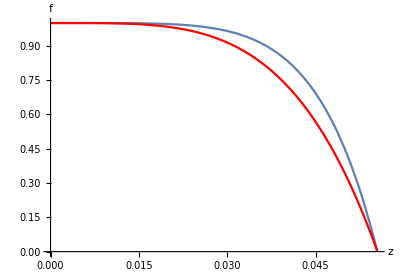

```mathematica
Show[ParametricPlot[{Exp[-A-2./3Log[λf[A]]]ΛUVh,ff[A]/fUVval},{A,1. 10^-6,25},AspectRatio->0.7,PlotRange->All,AxesLabel->{"z","f"}],Plot[(1-z^4/0.0555^4),{z,0,0.0555},PlotStyle->Red]]
```

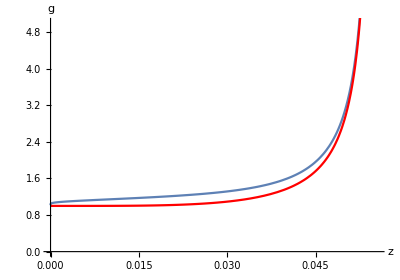

```mathematica
Show[ParametricPlot[{Exp[-A-2./3Log[λf[A]]]ΛUVh,qf[A]^2/ff[A]/(1+2/3 λf'[A]/λf[A])^2},{A,1. 10^-6,25},AspectRatio->0.7,PlotRange->{{0,0.0555},{0,5}},AxesLabel->{"z","g"}],Plot[1/(1-z^4/0.0555^4),{z,0,0.0555},PlotStyle->Red,PlotRange->{0,10}]]
```

Results at T~1.3 Tc

```mathematica
solFTB[0,0.,14.,10^-8,1.*10^-6,50.,1000.];
Tval
```

0.999391

```mathematica
TinMeV=0.9993910629387637/Tchere 270
```

345.893

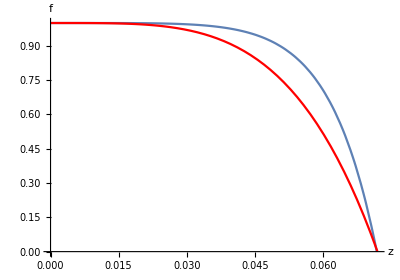

```mathematica
Show[ParametricPlot[{Exp[-A-2./3Log[λf[A]]]ΛUVh,ff[A]/fUVval},{A,1. 10^-6,25},AspectRatio->0.7,PlotRange->All,AxesLabel->{"z","f"}],Plot[(1-z^4/(.072)^4),{z,0,0.072},PlotStyle->Red]]
```

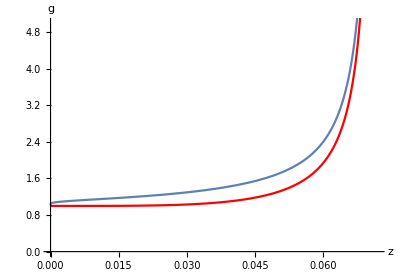

```mathematica
Show[ParametricPlot[{Exp[-A-2./3Log[λf[A]]]ΛUVh,qf[A]^2/ff[A]/(1+2/3 λf'[A]/λf[A])^2},{A,1. 10^-6,25},AspectRatio->0.7,PlotRange->{{0,0.072},{0,5}},AxesLabel->{"z","g"}],Plot[1/(1-z^4/0.072^4),{z,0,0.08},PlotStyle->Red,PlotRange->{0,10}]]
```

Results at T~Tc

```mathematica
solFTB[0,0.,22.5,10^-8,1.*10^-6,50.,1000.];
Tval
```

0.779326

```mathematica
TinMeV=0.7793258088888351/Tchere 270
```

269.727

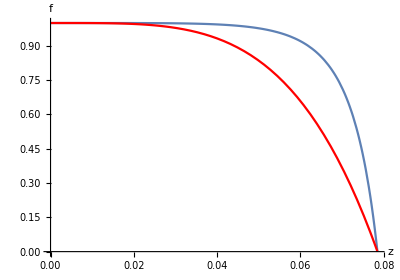

```mathematica
Show[ParametricPlot[{Exp[-A-2./3Log[λf[A]]]ΛUVh,ff[A]/fUVval},{A,1. 10^-6,25},AspectRatio->0.7,PlotRange->All,AxesLabel->{"z","f"}],Plot[(1-z^4/(.0785)^4),{z,0,0.0785},PlotStyle->Red]]
```

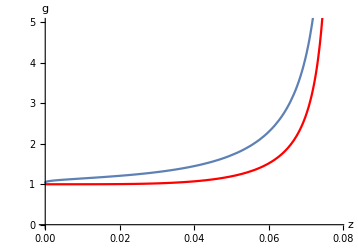

```mathematica
Show[ParametricPlot[{Exp[-A-2./3Log[λf[A]]]ΛUVh,qf[A]^2/ff[A]/(1+2/3 λf'[A]/λf[A])^2},{A,1. 10^-6,25},AspectRatio->0.7,PlotRange->{{0,0.0785},{0,5}},AxesLabel->{"z","g"}],Plot[1/(1-z^4/0.0785^4),{z,0,0.0785},PlotStyle->Red,PlotRange->{0,10}]]
```

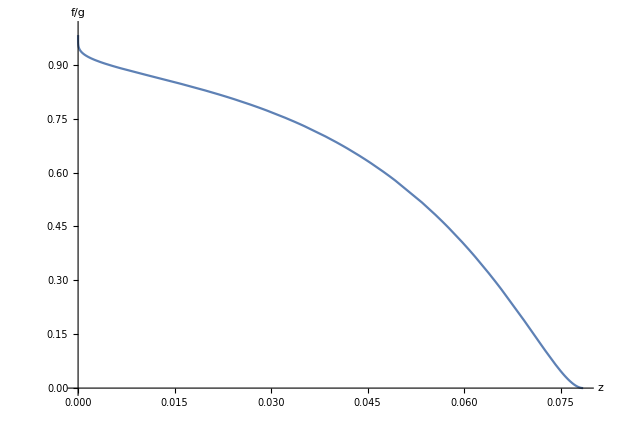

```mathematica
ParametricPlot[{Exp[-A-2./3Log[λf[A]]]ΛUVh,ff[A]/fUVval/(qf[A]^2/ff[A]/(1+2/3 λf'[A]/λf[A])^2)},{A,1. 10^-6,25},AspectRatio->0.7,PlotRange->{{0,0.0785},{0,1}},AxesLabel->{"z","f/g"}]
```

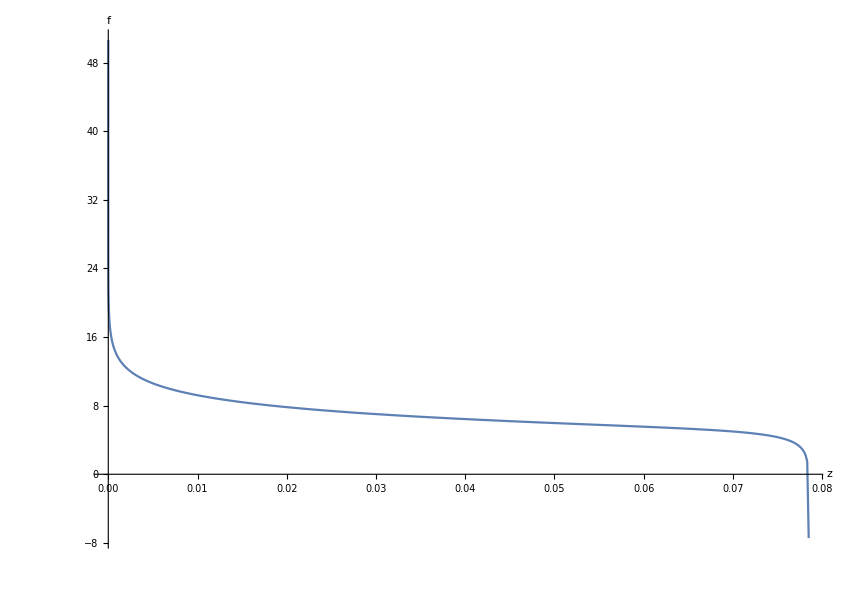

```mathematica
ParametricPlot[{Exp[-A-2./3Log[λf[A]]]ΛUVh,Log[(Exp[-A-2./3Log[λf[A]]]ΛUVh)^-2
ff[A]/fUVval]},{A,1. 10^-6,25},AspectRatio->0.7,PlotRange->All,AxesLabel->{"z","f"}]
```

```mathematica
Exp[-A-2./3Log[λf[A]]]ΛUVh/.A->1.*10^-6
```

0.0784925

```mathematica
Table[{Exp[-A-2./3Log[λf[A]]]ΛUVh,(Exp[-A-2./3Log[λf[A]]]ΛUVh)^-2
ff[A]/fUVval}]
```

{(0.625581 ⅇ^-A)/(Piecewise[{{InterpolatingFunction[…][A], A<50.}, {InterpolatingFunction[…][A], True}}])^0.666667,9.17946 ⅇ^(2 A) (Piecewise[{{InterpolatingFunction[…][A], A<50.}, {InterpolatingFunction[…][A], True}}])^1.33333 (Piecewise[{{InterpolatingFunction[…][A], A<50.}, {InterpolatingFunction[…][A], True}}])}

### Normalizing zh=1

Results at T~2 Tc

```mathematica
solFTB[0,0.,10.,10^-8,1.*10^-6,50.,1000.];
Tval
ΛUVh
```

1.50218

0.257482

Comparing to the “AdS” factors

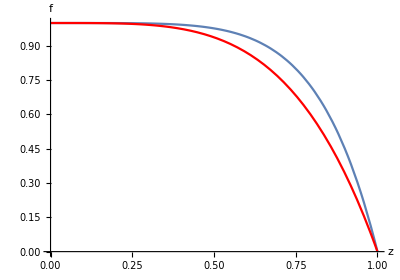

```mathematica
Show[ParametricPlot[{Exp[-A-2./3Log[λf[A]]]/Exp[-2./3Log[λf[1. 10^-6]]],ff[A]/fUVval},{A,1. 10^-6,25},AspectRatio->0.7,PlotRange->All,AxesLabel->{"z","f"}],Plot[(1-z^4),{z,0,1},PlotStyle->Red]]
```

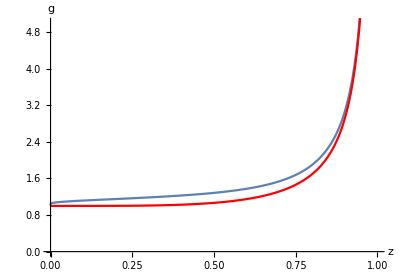

```mathematica
Show[ParametricPlot[{Exp[-A-2./3Log[λf[A]]]/Exp[-2./3Log[λf[1. 10^-6]]],qf[A]^2/ff[A]/(1+2/3 λf'[A]/λf[A])^2},{A,1. 10^-6,25},AspectRatio->0.7,PlotRange->{{0,1.},{0,5}},AxesLabel->{"z","g"}],Plot[1/(1-z^4),{z,0,1.},PlotStyle->Red,PlotRange->{0,10}]]
```

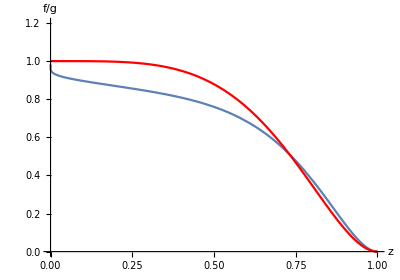

```mathematica
Show[ParametricPlot[{Exp[-A-2./3Log[λf[A]]]/Exp[-2./3Log[λf[1. 10^-6]]],ff[A]/fUVval(qf[A]^2/ff[A]/(1+2/3 λf'[A]/λf[A])^2)^-1},{A,1. 10^-6,25},AspectRatio->0.7,PlotRange->{{0,1.},{0,1.2}},AxesLabel->{"z","f/g"}],Plot[(1-z^4)^2,{z,0,1.},PlotStyle->Red,PlotRange->{0,10}]]
```

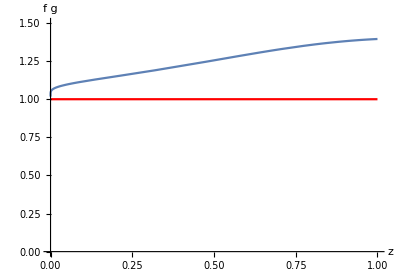

```mathematica
Show[ParametricPlot[{Exp[-A-2./3Log[λf[A]]]/Exp[-2./3Log[λf[1. 10^-6]]],(ff[A]/fUVval) qf[A]^2/ff[A]/(1+2/3 λf'[A]/λf[A])^2},{A,1. 10^-6,25},AspectRatio->0.7,PlotRange->{{0,1.},{0,1.5}},AxesLabel->{"z","f g"}],Plot[1,{z,0,1.},PlotStyle->Red,PlotRange->{0,10}]]
```

```mathematica
fzfun1=Interpolation[Table[{Exp[-A-2./3Log[λf[A]]]/Exp[-2./3Log[λf[1. 10^-6]]],ff[A]/fUVval}/.A->Exp[lA]-1.,{lA,1. 10^-6,Log[26.],Log[26.]/500.}]]
gzfun1=Interpolation[Table[{Exp[-A-2./3Log[λf[A]]]/Exp[-2./3Log[λf[1. 10^-6]]],qf[A]^2/ff[A]/(1+2/3 λf'[A]/λf[A])^2}/.A->Exp[lA]-1.,{lA,1. 10^-6,Log[26.],Log[26.]/5000.}]]
fgzfun1=Interpolation[Table[{Exp[-A-2./3Log[λf[A]]]/Exp[-2./3Log[λf[1. 10^-6]]],ff[A]/fUVval qf[A]^2/ff[A]/(1+2/3 λf'[A]/λf[A])^2}/.A->Exp[lA]-1.,{lA,1. 10^-6,Log[26.],Log[26.]/500.}]]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

Results at T~1.3 Tc

```mathematica
solFTB[0,0.,14.,10^-8,1.*10^-6,50.,1000.];
Tval
```

0.999391

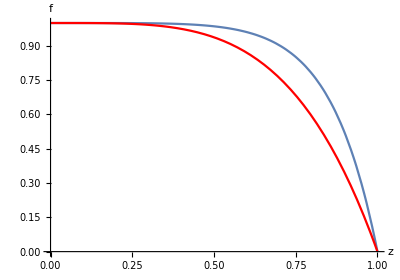

```mathematica
Show[ParametricPlot[{Exp[-A-2./3Log[λf[A]]]/Exp[-2./3Log[λf[1. 10^-6]]],ff[A]/fUVval},{A,1. 10^-6,25},AspectRatio->0.7,PlotRange->All,AxesLabel->{"z","f"}],Plot[(1-z^4),{z,0,1},PlotStyle->Red]]
```

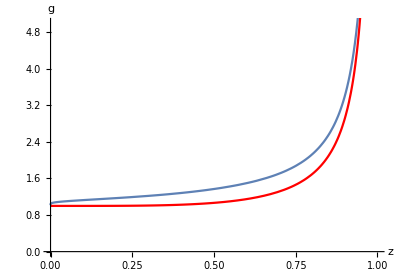

```mathematica
Show[ParametricPlot[{Exp[-A-2./3Log[λf[A]]]/Exp[-2./3Log[λf[1. 10^-6]]],qf[A]^2/ff[A]/(1+2/3 λf'[A]/λf[A])^2},{A,1. 10^-6,25},AspectRatio->0.7,PlotRange->{{0,1.},{0,5}},AxesLabel->{"z","g"}],Plot[1/(1-z^4),{z,0,1.},PlotStyle->Red,PlotRange->{0,10}]]
```

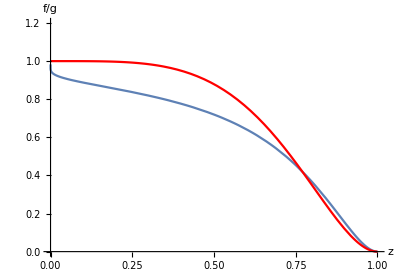

```mathematica
Show[ParametricPlot[{Exp[-A-2./3Log[λf[A]]]/Exp[-2./3Log[λf[1. 10^-6]]],ff[A]/fUVval(qf[A]^2/ff[A]/(1+2/3 λf'[A]/λf[A])^2)^-1},{A,1. 10^-6,25},AspectRatio->0.7,PlotRange->{{0,1.},{0,1.2}},AxesLabel->{"z","f/g"}],Plot[(1-z^4)^2,{z,0,1.},PlotStyle->Red,PlotRange->{0,10}]]
```

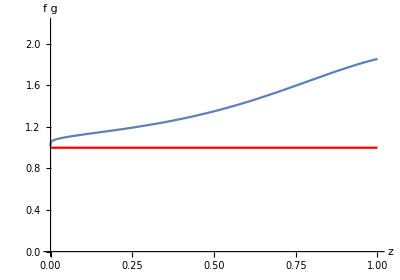

```mathematica
Show[ParametricPlot[{Exp[-A-2./3Log[λf[A]]]/Exp[-2./3Log[λf[1. 10^-6]]],(ff[A]/fUVval) qf[A]^2/ff[A]/(1+2/3 λf'[A]/λf[A])^2},{A,1. 10^-6,25},AspectRatio->0.7,PlotRange->{{0,1.},{0,2.2}},AxesLabel->{"z","f g"}],Plot[1,{z,0,1.},PlotStyle->Red,PlotRange->{0,10}]]
```

```mathematica
fzfun2=Interpolation[Table[{Exp[-A-2./3Log[λf[A]]]/Exp[-2./3Log[λf[1. 10^-6]]],ff[A]/fUVval}/.A->Exp[lA]-1.,{lA,1. 10^-6,Log[26.],Log[26.]/500.}]]
gzfun2=Interpolation[Table[{Exp[-A-2./3Log[λf[A]]]/Exp[-2./3Log[λf[1. 10^-6]]],qf[A]^2/ff[A]/(1+2/3 λf'[A]/λf[A])^2}/.A->Exp[lA]-1.,{lA,1. 10^-6,Log[26.],Log[26.]/5000.}]]
fgzfun2=Interpolation[Table[{Exp[-A-2./3Log[λf[A]]]/Exp[-2./3Log[λf[1. 10^-6]]],ff[A]/fUVval qf[A]^2/ff[A]/(1+2/3 λf'[A]/λf[A])^2}/.A->Exp[lA]-1.,{lA,1. 10^-6,Log[26.],Log[26.]/500.}]]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

Results at T~Tc

```mathematica
solFTB[0,0.,22.5,10^-8,1.*10^-6,50.,1000.];
Tval
```

0.779326

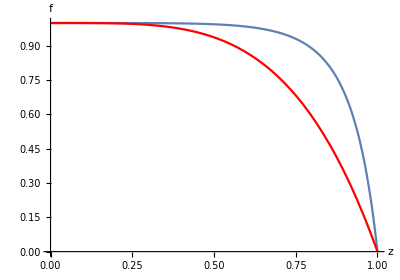

```mathematica
Show[ParametricPlot[{Exp[-A-2./3Log[λf[A]]]/Exp[-2./3Log[λf[1. 10^-6]]],ff[A]/fUVval},{A,1. 10^-6,25},AspectRatio->0.7,PlotRange->All,AxesLabel->{"z","f"}],Plot[(1-z^4),{z,0,1},PlotStyle->Red]]
```

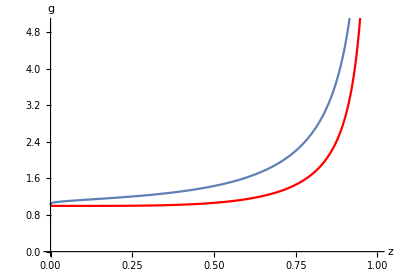

```mathematica
Show[ParametricPlot[{Exp[-A-2./3Log[λf[A]]]/Exp[-2./3Log[λf[1. 10^-6]]],qf[A]^2/ff[A]/(1+2/3 λf'[A]/λf[A])^2},{A,1. 10^-6,25},AspectRatio->0.7,PlotRange->{{0,1.},{0,5}},AxesLabel->{"z","g"}],Plot[1/(1-z^4),{z,0,1.},PlotStyle->Red,PlotRange->{0,10}]]
```

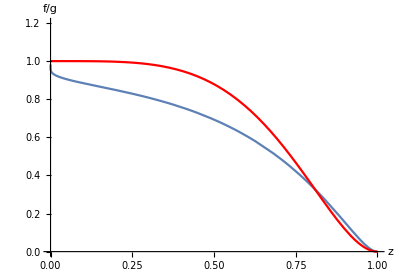

```mathematica
Show[ParametricPlot[{Exp[-A-2./3Log[λf[A]]]/Exp[-2./3Log[λf[1. 10^-6]]],ff[A]/fUVval(qf[A]^2/ff[A]/(1+2/3 λf'[A]/λf[A])^2)^-1},{A,1. 10^-6,25},AspectRatio->0.7,PlotRange->{{0,1.},{0,1.2}},AxesLabel->{"z","f/g"}],Plot[(1-z^4)^2,{z,0,1.},PlotStyle->Red,PlotRange->{0,10}]]
```

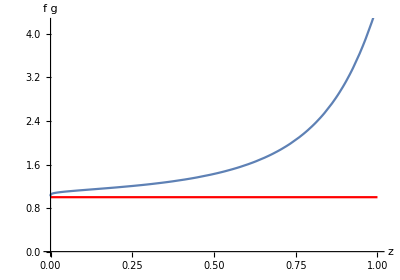

```mathematica
Show[ParametricPlot[{Exp[-A-2./3Log[λf[A]]]/Exp[-2./3Log[λf[1. 10^-6]]],(ff[A]/fUVval) qf[A]^2/ff[A]/(1+2/3 λf'[A]/λf[A])^2},{A,1. 10^-6,25},AspectRatio->0.7,PlotRange->{{0,1.},{0,4.2}},AxesLabel->{"z","f g"}],Plot[1,{z,0,1.},PlotStyle->Red,PlotRange->{0,10}]]
```

Example of interpolations. Interpolation of g has issues due to the pole. Better interpolate f*g...

```mathematica
fzfun3=Interpolation[Table[{Exp[-A-2./3Log[λf[A]]]/Exp[-2./3Log[λf[1. 10^-6]]],ff[A]/fUVval}/.A->Exp[lA]-1.,{lA,1. 10^-6,Log[26.],Log[26.]/500.}]]
```

InterpolatingFunction[…]

```mathematica
gzfun3=Interpolation[Table[{Exp[-A-2./3Log[λf[A]]]/Exp[-2./3Log[λf[1. 10^-6]]],qf[A]^2/ff[A]/(1+2/3 λf'[A]/λf[A])^2}/.A->Exp[lA]-1.,{lA,1. 10^-6,Log[26.],Log[26.]/5000.}]]
```

InterpolatingFunction[…]

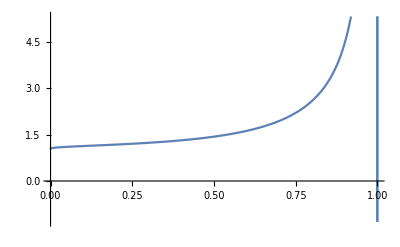

```mathematica
Plot[gzfun3[x],{x,1.3058783887824076*^-10,0.9999990000003622}]
```

```mathematica
fgzfun3=Interpolation[Table[{Exp[-A-2./3Log[λf[A]]]/Exp[-2./3Log[λf[1. 10^-6]]],ff[A]/fUVval qf[A]^2/ff[A]/(1+2/3 λf'[A]/λf[A])^2}/.A->Exp[lA]-1.,{lA,1. 10^-6,Log[26.],Log[26.]/500.}]]
```

InterpolatingFunction[…]

```mathematica
Clear[gzfun1,gzfun2,gzfun3]
gzfun1[z]=fgzfun1[z]/fzfun1[z];
gzfun2=fgzfun2/fzfun2;
gzfun3=fgzfun3/fzfun3;
```

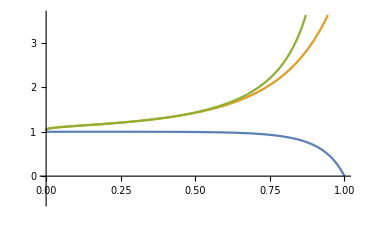

```mathematica
Plot[{fzfun3[z],fgzfun3[z],fgzfun3[z]/fzfun3[z]},{z,0,1.}]
```

Wilson loops: in the network code we use the following change of variables:

```mathematica
Clear[computeLIHQCD,computeVReg2IHQCD]
computeLIHQCD[fzfun_,fgzfun_,zs_]:=2/π NIntegrate[(zs y √(fgzfun[z]/fzfun[z]))/(√(fzfun[z]/((1-y^2)^4 fzfun[zs])-1))/.z->zs(1-y^2),{y,0,1}];computeVReg2IHQCD[fzfun_,fgzfun_,zs_]:=2π NIntegrate[(2 y)/(zs(1-y^2)^2)((√fgzfun[zs(1-y^2)])/(√(1-((1-y^2)^4 fzfun[zs])/fzfun[zs(1-y^2)]))-1),{y,0.001,√(1-10^-4/zs)}]-(2π)/zs;
```

But the original integrals in z-coordinate are the following, and they match the above equations:

```mathematica
computeLnetzIHQCD[fzfun_,fgzfun_,zs_]:=2/π NIntegrate[(√(fgzfun[z]/fzfun[z]))/(√((zs^4 fzfun[z])/(z^4 fzfun[zs])-1)),{z,0,zs}]
computeVnetzIHQCD[fzfun_,fgzfun_,zs_]:=2π NIntegrate[1/z^2((√fgzfun[z])/(√(1-(z^4 fzfun[zs])/(zs^4 fzfun[z])))-1),{z,10^-2,zs}]-(2π)/zs;
```

So let' s run with the z-coordinate

Note : here [1] = 520 Mev, [2] = 345 Mev and [3] = 270 Mev

```mathematica
sameSpacedGridSmall[in_,fin_,NPoints_:50]:=Table[in+(k (fin-in))/NPoints,{k,1,NPoints}]
```

```mathematica
gridzs=sameSpacedGridSmall[10^-8,0.99];
```

```mathematica
Clear[WLreg2]
WLreg2[1]=Table[{zs,computeLnetzIHQCD[fzfun1,fgzfun1,zs],computeVnetzIHQCD[fzfun1,fgzfun1,zs]},{zs,gridzs}];
WLreg2[2]=Table[{zs,computeLnetzIHQCD[fzfun2,fgzfun2,zs],computeVnetzIHQCD[fzfun2,fgzfun2,zs]},{zs,gridzs}];
WLreg2[3]=Table[{zs,computeLnetzIHQCD[fzfun3,fgzfun3,zs],computeVnetzIHQCD[fzfun3,fgzfun3,zs]},{zs,gridzs}];
```

Plot the potentials

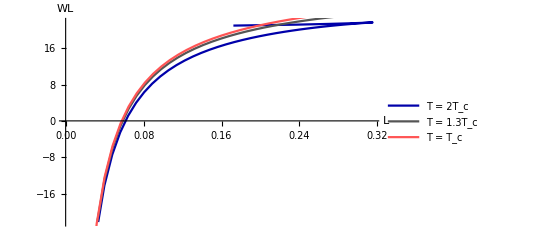

```mathematica
Show[ListLinePlot[Re@WLreg2[1][[All,{2,3}]],PlotStyle->Darker[Blue],PlotLegends->Placed[{"T = 2T_c"},{0.3,0.2}]],ListLinePlot[Re@WLreg2[2][[All,{2,3}]],PlotStyle->Darker[Gray],PlotLegends->Placed[{"T = 1.3T_c"},{0.6,0.2}]],ListLinePlot[Re@WLreg2[3][[All,{2,3}]],PlotStyle->Lighter[Red],PlotLegends->Placed[{"T = T_c"},{0.9,0.2}]],AxesLabel->{"L","WL"},BaseStyle->{Thick,FontSize->12},AxesStyle->Thick]
```

Plot the length wrt. turning point

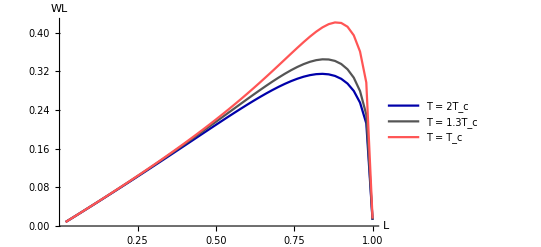

```mathematica
Show[ListLinePlot[Re@WLreg2[1][[All,{1,2}]],PlotStyle->Darker[Blue],PlotLegends->Placed[{"T = 2T_c"},{0.3,0.2}]],ListLinePlot[Re@WLreg2[2][[All,{1,2}]],PlotStyle->Darker[Gray],PlotLegends->Placed[{"T = 1.3T_c"},{0.6,0.2}]],ListLinePlot[Re@WLreg2[3][[All,{1,2}]],PlotStyle->Lighter[Red],PlotLegends->Placed[{"T = T_c"},{0.9,0.2}]],AxesLabel->{"z_*","L"},BaseStyle->{Thick,FontSize->12},AxesStyle->Thick,PlotRange->All]
```

```mathematica
Export["IHQCD-L(zs)-vs-network.pdf",%385,"PDF"]
```

/home/htakko/Dropbox/Own/deep-learning-EE/figures/IHQCD-L(zs)-vs-network.pdf

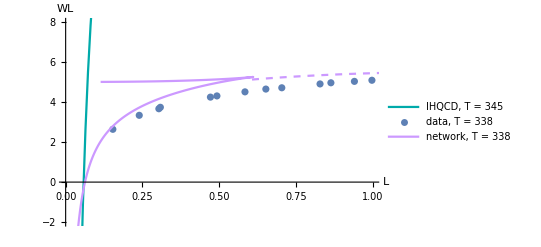

```mathematica
Show[ListLinePlot[Re@WLreg2[2][[All,{2,3}]],PlotStyle->Darker[Cyan],PlotLegends->Placed[{"IHQCD, T = 345"},Bottom]],ListPlot[{T2 fmToInvGeV[#⟦1⟧],Around[(#⟦2⟧)/T2,(#⟦3⟧)/T2]}&/@dataRe2,AxesLabel->{"T L","Re[V/T]"},PlotLegends->Placed[{"data, T = 338"},Bottom]],ListLinePlot[Table[Re@complexpotentials1607Reg2[T][[All,{2,3}]],{T,{338}}],PlotStyle->dashedStyleRainbow[[3;;]]],ListLinePlot[Table[Re@potentials1607Reg2[T][[All,{2,3}]],{T,{338}}],PlotStyle->styleRainbow[[3;;]],PlotLegends->Placed[{"network, T = 338"},Bottom]],BaseStyle->{Thick,FontSize->12},AxesStyle->Thick,AxesOrigin->{0,0},{PlotRange->{{0,1.},{-2,8}}},AxesLabel->{"L","WL"}]
```

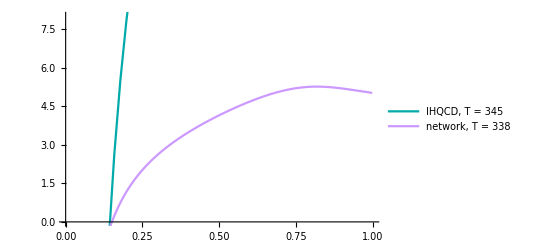

```mathematica
Show[ListLinePlot[Re@WLreg2[2][[All,{1,3}]],PlotStyle->Darker[Cyan],PlotLegends->Placed[{"IHQCD, T = 345"},Bottom]],ListLinePlot[Table[Re@potentials1607Reg2[T][[All,{1,3}]],{T,{338}}],PlotStyle->styleRainbow[[3;;]],PlotLegends->Placed[{"network, T = 338"},Bottom]],BaseStyle->{Thick,FontSize->12},AxesStyle->Thick,AxesOrigin->{0,0},{PlotRange->{{0,1.},{0,8}}}]
```

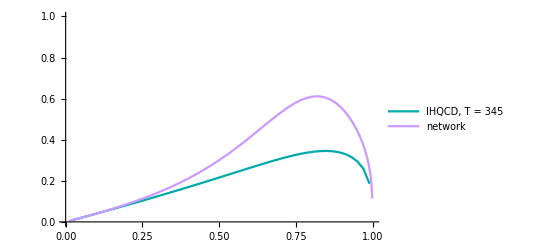

```mathematica
Show[ListLinePlot[Re@WLreg2[2][[All,{1,2}]],PlotStyle->Darker[Cyan],PlotLegends->Placed[{"IHQCD, T = 345"},Bottom]],ListLinePlot[Table[Re@potentials1607Reg2[T][[All,{1,2}]],{T,{338}}],PlotStyle->styleRainbow[[3;;]],PlotLegends->Placed[{"network"},Bottom]],BaseStyle->{Thick,FontSize->12},AxesStyle->Thick,AxesOrigin->{0,0},{PlotRange->{{0,1.},{0,1}}}]
```

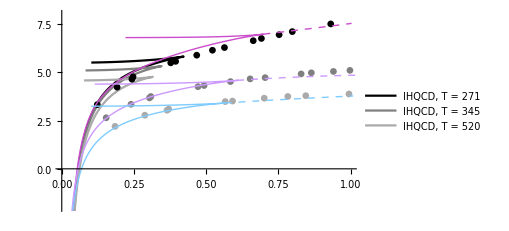

```mathematica
Show[ListLinePlot[Re@WLreg2[3][[All,{2,3}]],PlotStyle->Black,PlotLegends->Placed[{"IHQCD, T = 271"},Top]],ListLinePlot[Re@WLreg2[2][[All,{2,3}]],PlotStyle->Gray,PlotLegends->Placed[{"IHQCD, T = 345"},Top]],ListLinePlot[Re@WLreg2[1][[All,{2,3}]],PlotStyle->Lighter[Gray],PlotLegends->Placed[{"IHQCD, T = 520"},Top]],ListPlot[{T1 fmToInvGeV[#⟦1⟧],Around[(#⟦2⟧)/T1,(#⟦3⟧)/T1]}&/@dataRe,AxesLabel->{"T L","Re[V/T]"},PlotLegends->Placed[{"data, T = 271"},Bottom],PlotStyle->Black],ListPlot[{T2 fmToInvGeV[#⟦1⟧],Around[(#⟦2⟧)/T2,(#⟦3⟧)/T2]}&/@dataRe2,AxesLabel->{"T L","Re[V/T]"},PlotLegends->Placed[{"data, T = 338"},Bottom],PlotStyle->Gray],ListPlot[{T3 fmToInvGeV[#⟦1⟧],Around[(#⟦2⟧)/T3,(#⟦3⟧)/T3]}&/@dataRe3,AxesLabel->{"T L","Re[V/T]"},PlotLegends->Placed[{"data, T = 406"},Bottom],PlotStyle->Lighter[Gray]],ListLinePlot[Table[Re@complexpotentials1607Reg2[T][[All,{2,3}]],{T,{271,338,406}}],PlotStyle->dashedStyleRainbow[[2;;]]],ListLinePlot[Table[Re@potentials1607Reg2[T][[All,{2,3}]],{T,{271,338,406}}],PlotStyle->styleRainbow[[2;;]],PlotLegends->Placed[{"network, T = 271","network, T = 338","network, T = 406"},Right]],BaseStyle->{Thick,FontSize->12},AxesStyle->Thick,AxesOrigin->{0,0},{PlotRange->{{0,1.},{-2,8}}}]
```

Save the IHQCD potential as data file to test the machine learning code: The data needs to be in form
[[1]] = T * L (this is equal to T* fmToInvGev(l))
[[2]] = (Re(v))/T
[[3]] = (Re(σ))/T(the error bars, this we do not have, set to 0)
[[4]] = (Im(v))/T
[[5]] = (Im(σ))/T (the error bars for imag part, we don’t have so set to 0)

For the paper:
- leave EE out
- to